```mathematica
(* taken from wolfram demos for binomial confidence intervals: http://demonstrations.wolfram.com/ConfidenceIntervalsForTheBinomialDistribution *)
```

```mathematica
(* j is successes, n is trials (attempts, samples ), p is probably the confidence? *) 
b[j_,n_,p_]:=CDF[BinomialDistribution[n,p],j];
intervals[jj_,nn_,confLvl_, opts___]:=Module[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2],
blueSquare=Graphics[{Blue,Rectangle[]},ImageSize->10],redSquare=Graphics[{Red,Rectangle[]},ImageSize->10],blackSquare=Graphics[{Black,Rectangle[]},ImageSize->10],izq,der,interWald,interWilson,nums,int1,int2,int3,std,corrnums,stimes},
izq=Quiet@If[jj==1,0,(p/.NSolve[1-b[jj-1,nn,p]==(1-confLvl)/2,p])[[1]]];der=Quiet@(p/.NSolve[b[jj,nn,p]==(1-confLvl)/2,p])[[1]];
interWald=Max[0,#]&/@{jj/nn -t025  √(jj/nn (1-jj/nn)/nn),jj/nn +t025  √(jj/nn (1-jj/nn)/nn)};
interWilson={1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2-t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2))),1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2+t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2)))};int1=interWald;
int2=interWilson;
int3={izq,der};nums={interWald,interWilson,{izq,der}};
std=StringDrop[#,1]&/@(ToString/@(PaddedForm[#,{3,3}]&/@Flatten[nums]));difs=#[[2]]-#[[1]]&/@nums;
az=StringDrop[#,1]&/@(ToString/@(PaddedForm[#,{3,3}]&/@difs));
corrnums=Table["["<>std[[j]]<>","<>" "<>std[[j+1]]<>"]",{j,1,Length[std]-1,2}];stimes=Text[#]&/@Table[corrnums[[j]]<>"      "<>az[[j]],{j,1,3}];
ListLinePlot[{{jj/nn,0},{jj/nn,0.003}},Axes->{True,False},AxesOrigin->{0.25,0},PlotStyle->{Black,Thickness[0.001]},PlotRange->{{0,1},{-0.002,0.009}},Epilog->{Text[Style["j/n",Italic,Medium],{jj/nn,-0.00075}],Inset[Grid[{{Style[StringJoin[ToString[confLvl*100],"% confidence intervals"],Medium]},{Style["for the probability parameter",Medium]},{Style["in a binomial distribution",Medium]}}],{0.5,0.008}],Inset[Grid[{{Text["method"],Text[""],Text["  interval           length"]},{Text["conventional"],blueSquare,stimes[[1]]},{Text["Wilson"],redSquare,stimes[[2]]},{Text["Clopper-Pearson"],blackSquare,stimes[[3]]}}],{0.5,0.005}],Thick,Blue,Line@MapThread[List,{int1,{0.003,0.003}}],Thick,Red,Line@MapThread[List,{int2,{0.002,0.002}}],Thick,Black,Line@MapThread[List,{int3,{0.001,0.001}}]},opts]]
```

```mathematica
Manipulate[
If[successes>tries-2,successes=tries-2];
intervals[successes,tries,confidence, ImageSize->550],
{{successes,10},1,tries-2,1,Appearance->"Labeled"},
{{tries,50},20,200,5,Appearance->"Labeled"},{{confidence,0.95},0.5,0.99,0.01,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
(* redefining Wald CI for convenience *) 
interWald[jj_, nn_,confLvl_]:=With[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2]},Interval[Max[0,#]&/@{jj/nn -t025  √(jj/nn (1-jj/nn)/nn),jj/nn +t025  √(jj/nn (1-jj/nn)/nn)}]];
```

```mathematica
(* redefining Wilson CI for convenience *) 
interWilson[jj_, nn_,confLvl_]:=With[{t025=Quantile[NormalDistribution[],1 - (1-confLvl)/2]}, Interval[{1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2-t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2))),1/(1+t025^2/nn)(jj/nn+1/(2 nn) t025^2+t025 √((jj/nn (1-jj/nn))/nn+t025^2/(4 nn^2)))}]]
```

```mathematica
(*** FILE MANIPULATIONS ***)
```

```mathematica
(* useful def*)
dataDirPath = "~/Dropbox/upenn/research/aa/monitoring_data/data/Session_4_Sonar_Nocontroller_8Aug2019/";
```

```mathematica
monFilenames[winSize_, idpairlist_] := StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/mon", ToString[#[[2]]], "_",ToString[winSize], "/iter", ToString[#[[1]]], "_mondet", ToString[#[[2]]], "_",ToString@winSize, "_estrates.txt"] & /@idpairlist;

allMonFilenames[winSize_] := StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/mon", ToString[#[[2]]], "_",ToString[winSize], "/iter", ToString[#[[1]]], "_mondet", ToString[#[[2]]], "_",ToString@winSize, "_estrates.txt"] & /@Flatten[Outer[List, Range[1,5], Range[1,5]], 1];

detFilenames[idpairlist_] := StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/det", ToString[#[[2]]], "/iter", ToString[#[[1]]], "_both_det_estrates.txt"] & /@idpairlist;

allDetFilenames = StringJoin[dataDirPath, "Iteration_", ToString[#[[1]]], "/det", ToString[#[[2]]], "/iter", ToString[#[[1]]], "_both_det_estrates.txt"] & /@Flatten[Outer[List, Range[1,5], Range[1,5]], 1];

(* add up a given field's values over filenames *) 
countFromFiles[fieldName_, filenames_] := Plus@@(*list of frame numbers from each*)(getValueFromListOfPairs[#,fieldName]& /@ (*list of all stat dicts*) (nameValuePairsFromFile/@filenames(*list of filenames*)))
```

```mathematica
(* various counts from mons *) 
allMonH1ct = countFromFiles[ "h1count",allMonFilenames[10]]
allMonFNct = countFromFiles[ "FNcount",allMonFilenames[10]]
allDetH0ct =countFromFiles[ "h0count",allDetFilenames]
allDetFPct =countFromFiles[ "FPcount",allDetFilenames]
```

580

389

1000

110

```mathematica
(* PREDICTIONS *) 
predFNR[detFPR_, monWin_, pDetNCH0_:0(* for here *)] := 1 - (1-detFPR)(1 - detFPR - pDetNCH0)^(monWin-1);
```

```mathematica
subsetCt = Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1]] - 1;
subsetCt23to25 = Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {23,25}];
subsetCt20to25 = Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {20,25}];
```

```mathematica
(* COMPARISON: prediction vs data-driven CI *) 
(* one shot *) 
IntervalMemberQ[(* interval *) interWilson[countFromFiles[ "FNcount",allMonFilenames[10]], countFromFiles[ "h1count",allMonFilenames[10]], 0.95], (* prediction *) predFNR[countFromFiles[ "FPcount",allDetFilenames]/countFromFiles[ "h0count",allDetFilenames], 10]]
```

True

```mathematica
oneIntervalTest[pairIdList_] := IntervalMemberQ[(* interval *) interWilson[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[countFromFiles[ "FPcount",detFilenames[pairIdList]]/countFromFiles[ "h0count",detFilenames[pairIdList]], 10]];
```

```mathematica
oneIntervalTestPair[pairIdList_] := {(* interval *) interWilson[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[countFromFiles[ "FPcount",detFilenames[pairIdList]]/countFromFiles[ "h0count",detFilenames[pairIdList]], 10]};
```

```mathematica
(* testing over subsets of 23+ -- very favorable, around 1%. *) 
Tally[oneIntervalTest[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {23, 25}]]
{{True,323},{False,3}}
```

{{True,323},{False,3}}

```mathematica
(* wow terrible stuff on small data, 15-20% error out of 100: *) 
Tally[oneIntervalTest[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ RandomInteger[{1,subsetCt},100]]
```

{{{True},83},{{False},17}}

```mathematica
(* but good on big data, 0-2% error out of 100, weird: *)
```

```mathematica
Tally[oneIntervalTest[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {23,25},{#}] &/@ RandomInteger[{1,subsetCt23to25},100]]
```

{{{True},100}}

```mathematica
(* medium data? 5-15% error out of 100 *)
```

```mathematica
Tally[oneIntervalTest[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {20,25},{#}] &/@ RandomInteger[{1,subsetCt20to25},100]]
```

{{{True},92},{{False},8}}

```mathematica
(** randomized sampling, no constraints on subset size *) 

(* a list of pairs {subset size, whether CI contains the prediciton} *) 
generatePredvsCISample[sampleCt_]:= ({#[[1]],oneIntervalTest[#[[2]]]}&/@( Flatten[{Length@#, #} &/@(* list of lists of subsets possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*all subsets *)subsetCt
},sampleCt],1]));

(* triples of {subsetsize, # of trues at that size, # of falses at that size} *)
tallyUpPredvsCISample[sample_]:= With[ {trueCt= Count[sample, {#, True}], falseCt= Count[sample, {#, False}]} , {#,trueCt, falseCt}]& /@  Range[1,25];

(* converting tallied triples to ratios and stdev, getting pairs {subset size, accuracy w/uncert based on wilson CIs} *) 
generatePredvsCIOutcomes[sampleCt_]:={(*subset size*) #[[1]], (*ratio of successes to total *) With[{est = #[[2]]/(#[[2]]+#[[3]]), int = interWilson[#[[2]],#[[2]]+#[[3]], 0.95]},Around[(*estimated accuracy*)est,(* converting wilson interval to uncertainty bounds*) {Min@int-est, Max@int-est}]] }&/@ (* getting tallied sample data and filtering it*)Select[tallyUpPredvsCISample[generatePredvsCISample[sampleCt]], #[[2]] >0 ∨ #[[3]]>0 # &];
```

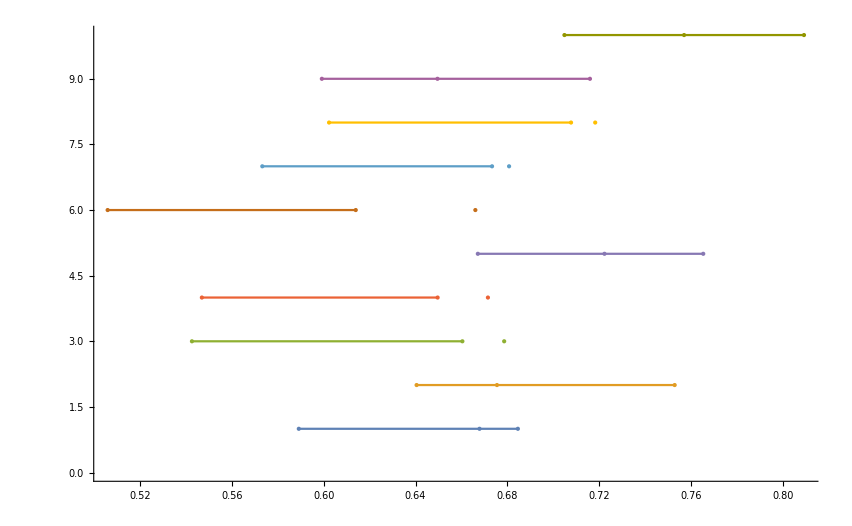

```mathematica
(*** VISUALS for PRED vs DATA-DRIVEN  ***) 

(* just a few samples *)
(* across all possible data -- poor performance *)
NumberLinePlot[oneIntervalTestPair[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ RandomInteger[{1,subsetCt},10], PlotStyle->PointSize[Large]]
```

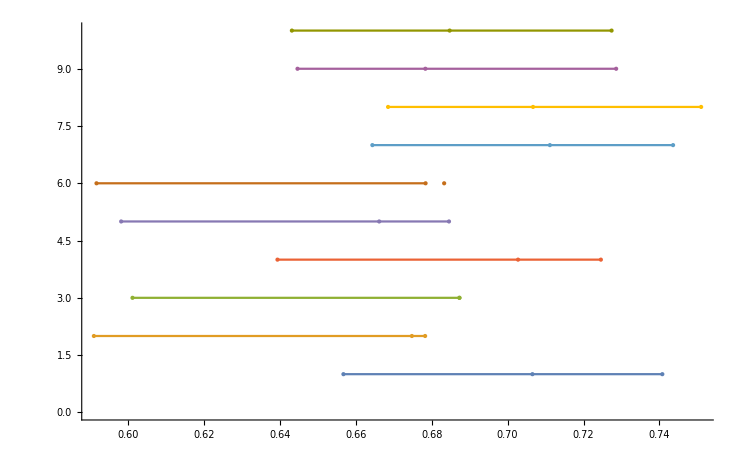

```mathematica
NumberLinePlot[oneIntervalTestPair[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {20,25},{#}] &/@ RandomInteger[{1,subsetCt20to25},10], PlotStyle->PointSize[Large]]
```

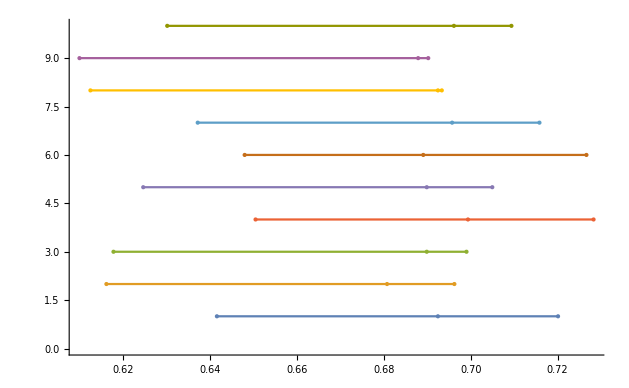

```mathematica
(* when substantial data is given -- good performance *)
NumberLinePlot[oneIntervalTestPair[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {23,25},{#}] &/@ RandomInteger[{1,subsetCt23to25},10], PlotStyle->PointSize[Large]]
```

```mathematica
(* is the above right? why are confidence intervals not shrinking substantially?? in larger data *)
```

```mathematica
(* big samples *) 
generateSuccessCountsPerSubsetSize := With[{subsetsCt = #},
(* count truths *)Count[oneIntervalTest[#]&/@ (* all possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*counting subsets *)Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt}]
},100], {True}]
]& /@ Range[1, 24];
```

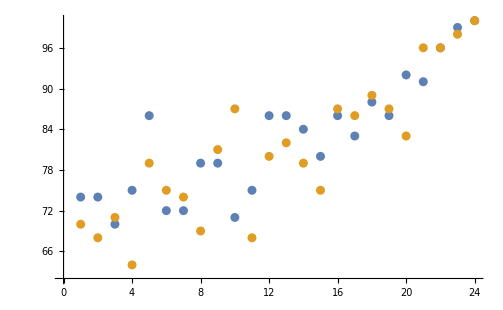
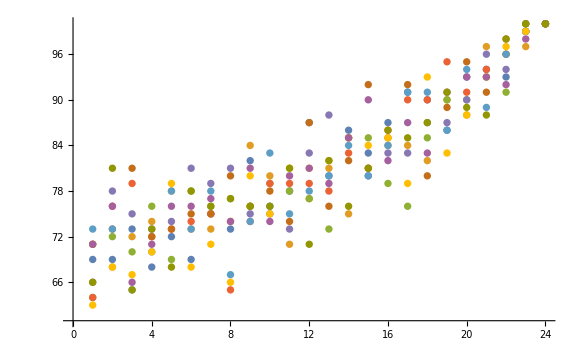
```mathematica
(* get 100 random samples for every size of the subset, return the number of times the estimate is in the interval *)
reslist2= {70,68,71,64,79,75,74,69,81,87,68,80,82,79,75,87,86,89,87,83,96,96,98,100};
reslist1= {74,74,70,75,86,72,72,79,79,71,75,86,86,84,80,86,83,88,86,92,91,96,99,100};
(* get 10 lists of 100 samples like above *) 
reslists10 = Table[generateSuccessCountsPerSubsetSize, 10]
reslists10= {{69,69,73,68,72,69,75,73,82,76,78,87,80,86,83,87,91,90,86,93,94,93,100,100},{71,68,72,74,78,73,73,74,84,80,71,77,81,75,81,84,84,82,90,88,97,96,97,100},{64,72,70,76,69,78,76,77,76,79,78,77,73,85,85,79,76,85,90,90,93,91,99,100},{64,76,79,72,73,74,75,65,74,79,79,79,78,83,81,86,90,90,95,91,94,98,99,100},{66,78,75,73,74,81,79,81,75,75,73,83,88,85,80,83,83,87,87,90,96,94,99,100},{71,73,81,72,73,75,75,80,76,78,74,87,76,82,92,85,92,80,89,95,91,96,100,100},{73,73,65,70,78,73,78,67,74,83,75,78,80,84,80,84,91,91,86,94,89,96,99,100},{63,68,67,70,79,68,71,66,80,75,81,81,82,85,84,85,79,93,83,88,93,97,99,100},{71,76,66,71,76,76,77,74,81,74,80,81,79,85,90,82,87,83,91,93,93,92,98,100},{66,81,65,73,68,78,76,77,76,76,81,71,82,76,81,86,85,87,91,89,88,98,100,100}};
(* visualize 2 lists *)
ListPlot[Inner[List, Range[1,24], #, List]& /@ {reslist1, reslist2}]
-Graphics-
(* visualize 10 lists *) 
ListPlot[Inner[List, Range[1,24], #, List]& /@ reslists10]
-Graphics-
(* get 100 lists of 100 samples like above *) 
reslists100 = Table[generateSuccessCountsPerSubsetSize, 100]
```

```mathematica
reslists100 = {{73,77,67,80,75,74,82,78,83,72,86,77,74,81,83,79,83,92,89,87,93,94,99,100},{58,77,68,76,77,72,74,74,83,76,79,78,77,75,83,85,86,88,90,95,95,96,100,100},{68,74,67,67,66,78,68,84,76,85,77,80,77,81,83,75,87,83,93,92,96,98,99,100},{68,71,70,74,73,76,73,72,73,82,85,83,81,83,82,90,93,82,92,91,95,93,98,100},{68,78,77,78,77,68,78,73,65,75,81,82,79,80,88,79,84,89,89,88,93,95,99,100},{69,79,76,70,80,78,77,72,82,69,75,83,83,86,83,88,89,91,89,91,98,94,98,100},{71,77,73,77,74,72,74,68,82,81,82,87,83,80,92,78,85,87,91,92,96,95,99,100},{68,73,69,71,76,71,76,79,80,83,74,81,80,84,83,87,86,85,88,93,88,97,98,100},{65,82,70,73,76,69,75,78,75,86,81,82,78,79,83,84,89,88,95,88,92,97,98,100},{68,73,75,82,70,74,75,84,76,75,82,83,72,78,79,85,90,81,93,90,90,96,97,100},{69,68,65,75,80,80,72,75,78,74,71,77,80,86,81,84,86,86,90,91,92,96,98,100},{67,79,62,71,66,78,80,81,78,77,75,86,83,80,89,78,90,82,89,87,93,96,98,100},{65,75,65,70,81,74,77,77,72,78,82,77,88,85,88,87,82,87,91,95,92,92,98,100},{63,79,70,73,77,76,78,71,79,75,82,75,79,83,82,82,89,88,90,88,93,98,100,100},{73,76,69,75,72,66,78,76,78,69,83,75,75,81,76,88,87,85,88,87,90,96,99,100},{59,73,71,72,70,72,76,75,74,83,84,90,82,82,85,86,81,86,89,95,94,95,99,100},{68,78,73,78,75,81,69,82,81,82,81,80,83,83,87,83,84,89,90,95,92,96,99,100},{73,77,72,77,72,75,76,76,76,76,86,80,89,83,79,92,88,87,86,90,90,91,99,100},{62,73,73,66,69,75,75,74,76,83,80,79,80,85,82,84,89,93,87,91,91,95,97,100},{74,73,72,69,70,72,71,79,68,81,79,79,81,78,81,84,81,89,90,86,94,98,100,100},{65,78,70,80,75,83,77,77,73,81,86,74,90,84,92,84,86,88,93,90,91,97,99,100},{63,82,69,80,80,80,77,77,73,77,79,86,87,85,87,86,83,85,90,90,88,96,99,100},{68,70,65,76,79,74,68,79,76,79,74,80,84,79,82,89,83,90,87,92,93,95,100,100},{73,72,77,77,70,65,69,78,78,81,80,81,75,82,83,81,82,86,88,89,93,99,97,100},{72,78,75,70,72,80,68,75,79,75,81,82,86,83,85,84,94,84,91,93,91,96,98,100},{69,66,70,71,67,67,72,75,78,84,86,79,76,79,85,91,87,88,89,96,95,94,100,100},{72,68,71,75,66,71,75,75,72,74,83,84,83,82,81,84,82,88,91,87,94,97,100,100},{71,69,68,73,75,73,78,81,83,80,82,74,79,87,88,81,86,87,92,87,93,92,98,100},{72,74,63,70,72,77,71,71,76,83,79,82,86,86,84,82,82,87,85,95,93,97,100,100},{63,78,70,78,74,78,73,81,70,84,71,82,79,81,82,83,87,87,85,91,92,97,99,100},{68,77,72,75,79,70,77,78,79,79,76,79,81,84,90,85,85,88,89,92,84,98,100,100},{72,72,77,74,79,62,75,74,79,76,76,81,81,88,79,86,87,83,87,92,97,96,99,100},{67,73,72,70,78,71,67,75,79,78,81,82,83,82,83,86,85,87,88,83,92,97,98,100},{75,77,67,72,80,75,74,68,74,83,84,77,86,76,91,87,90,85,88,91,94,94,100,100},{67,77,71,76,76,71,77,80,80,79,84,79,83,83,77,83,83,89,85,90,94,95,100,100},{65,72,62,69,81,74,79,76,74,82,82,78,82,87,84,85,89,91,89,96,94,93,99,100},{70,79,71,71,75,76,68,74,74,86,79,77,80,86,82,86,87,86,95,92,92,96,99,100},{65,76,70,66,72,74,77,76,78,78,81,76,87,79,86,81,84,86,86,89,89,95,100,100},{59,77,70,64,69,76,67,83,71,79,82,79,80,84,82,81,87,89,85,90,94,95,98,100},{64,72,67,80,71,77,70,75,71,78,78,77,81,82,83,89,85,86,89,92,92,97,98,100},{61,68,68,74,65,80,69,73,75,77,71,81,74,76,83,81,78,85,93,91,95,94,99,100},{63,73,81,76,77,73,78,73,75,82,77,87,73,82,84,83,80,81,92,91,96,97,99,100},{65,65,71,72,69,68,74,82,86,80,70,84,86,76,86,83,88,82,92,88,94,96,99,100},{76,73,75,68,75,77,77,77,74,74,79,75,79,86,84,77,84,89,88,91,91,94,100,100},{67,71,72,73,73,78,74,76,79,86,74,79,81,76,78,77,93,87,89,90,87,90,97,100},{67,70,61,70,75,79,76,76,77,81,87,85,82,83,77,87,84,95,95,89,91,94,98,100},{66,68,74,76,78,77,71,72,79,85,80,86,83,83,84,87,90,87,90,91,96,95,99,100},{66,75,77,59,66,66,75,69,80,71,86,83,84,83,79,83,91,83,89,92,91,95,99,100},{65,74,74,74,69,74,71,75,75,81,84,75,85,85,79,86,88,89,90,91,90,98,100,100},{61,70,71,76,69,73,75,79,85,72,73,86,85,81,81,85,85,89,90,89,93,96,99,100},{78,75,70,70,74,85,82,78,72,74,74,77,83,80,74,87,84,88,90,87,93,98,99,100},{54,75,75,72,78,75,80,79,75,73,75,80,82,78,80,87,87,88,89,90,98,94,100,100},{76,74,71,71,70,76,81,74,81,74,79,77,86,82,85,87,90,90,91,89,95,93,98,100},{72,70,77,69,80,69,69,73,75,68,77,83,74,83,85,85,84,84,89,94,95,94,98,100},{72,62,80,77,74,83,82,80,76,83,72,82,82,86,82,83,84,86,84,85,99,95,99,100},{64,77,71,74,80,78,73,74,73,79,78,82,83,80,86,83,89,84,90,89,94,97,100,100},{69,74,75,65,72,74,72,71,77,67,79,82,78,82,87,87,89,85,90,91,99,99,100,100},{77,68,70,72,76,66,79,78,77,73,76,84,83,67,82,83,86,83,87,92,97,95,99,100},{71,76,74,70,73,80,73,67,77,75,76,70,76,81,84,82,84,88,91,90,96,96,98,100},{71,63,76,69,68,83,76,85,79,82,78,83,83,80,84,81,83,81,85,89,94,97,99,100},{68,76,69,78,70,78,71,77,74,80,85,80,84,74,79,84,89,82,86,90,93,99,99,100},{71,68,68,79,72,78,81,68,76,86,78,76,82,82,83,85,86,88,87,90,94,97,99,100},{74,76,72,69,75,73,80,82,71,79,75,75,80,76,80,86,86,85,91,89,86,97,98,100},{72,75,71,73,74,77,69,82,81,71,77,79,84,79,84,90,90,92,88,91,94,97,98,100},{72,78,74,70,75,66,75,78,85,80,78,79,81,80,85,87,78,88,91,95,92,97,100,100},{76,66,63,67,76,75,74,70,72,73,86,88,80,83,83,84,88,87,89,95,93,97,98,100},{72,70,70,73,70,78,80,73,75,86,79,82,81,88,88,87,87,90,95,94,91,96,97,100},{67,72,65,70,73,86,71,79,86,79,74,85,77,86,90,84,80,88,87,86,86,95,97,100},{68,75,76,78,76,75,65,81,81,83,81,80,81,85,94,87,81,88,91,94,88,95,98,100},{67,64,69,72,69,77,77,78,76,81,81,82,87,84,85,87,85,85,84,94,95,93,100,100},{68,77,72,68,72,71,81,79,78,77,84,83,78,85,87,87,82,87,96,90,96,95,99,100},{65,75,71,68,77,71,69,80,76,83,74,80,83,79,87,87,84,85,90,94,90,96,100,100},{77,67,76,69,77,75,79,74,76,80,69,82,84,81,85,86,89,84,91,92,90,97,98,100},{76,76,70,63,72,74,78,76,77,78,87,84,84,76,77,83,89,92,88,86,97,96,99,100},{61,71,65,65,76,75,76,82,76,74,81,79,81,86,85,83,90,85,91,93,93,94,99,100},{65,74,68,70,77,79,71,80,82,82,76,83,86,82,86,84,86,93,91,92,94,97,99,100},{65,72,64,73,66,76,79,74,80,72,77,74,80,89,83,77,89,84,86,93,91,95,100,100},{67,70,65,62,69,68,74,74,73,73,77,79,82,83,83,82,81,87,91,82,96,95,99,100},{74,71,78,68,71,71,74,71,81,79,76,78,80,87,83,83,87,87,86,90,90,98,99,100},{61,78,81,79,68,81,74,74,84,78,79,79,82,92,81,86,84,83,92,87,94,97,99,100},{62,76,65,77,72,77,68,72,75,76,79,75,84,81,83,84,86,89,93,96,91,97,98,100},{76,67,79,69,65,71,76,74,76,76,81,81,84,82,77,87,85,90,92,90,96,94,97,100},{75,69,69,73,74,74,73,72,81,80,81,81,77,81,81,89,85,87,95,95,94,96,100,100},{73,73,77,69,66,73,73,67,77,77,82,77,74,87,81,86,90,92,93,90,91,93,99,100},{65,67,70,70,68,76,63,77,77,71,80,77,79,86,82,88,82,91,90,94,93,97,98,100},{65,71,70,82,73,73,76,71,74,79,83,80,87,83,77,87,81,91,91,91,93,96,97,100},{64,77,76,71,70,78,76,75,84,75,83,75,85,88,82,88,84,91,89,89,96,95,100,100},{73,68,68,73,81,82,73,74,73,73,83,82,77,84,79,83,84,89,89,92,94,95,98,100},{63,60,74,74,67,71,76,68,71,75,75,78,80,84,79,78,76,90,89,91,97,95,99,100},{68,77,75,79,76,75,75,75,73,86,84,80,81,84,79,87,82,84,95,94,88,97,99,100},{72,71,63,79,61,69,80,80,79,80,86,81,84,83,83,92,89,90,85,86,95,97,100,100},{69,73,71,75,72,79,78,78,67,77,82,77,78,81,82,93,84,86,89,96,95,96,99,100},{74,69,73,69,71,82,64,77,72,82,82,77,83,83,84,89,80,90,89,93,95,96,97,100},{69,70,78,66,78,80,77,78,71,79,81,76,78,79,86,84,88,92,89,93,97,97,98,100},{72,78,75,77,71,78,82,75,78,82,76,88,81,78,82,85,88,85,91,88,93,92,99,100},{68,66,73,68,76,73,77,76,73,81,77,75,81,77,83,88,82,85,88,96,89,99,99,100},{57,78,70,76,76,76,75,76,73,78,81,83,88,84,87,86,89,91,93,92,92,95,99,100},{67,65,71,80,68,79,76,71,73,73,80,81,83,77,87,80,86,91,82,89,91,97,98,100},{67,75,70,79,73,70,74,79,73,84,79,81,85,77,81,84,85,80,94,88,94,93,99,100},{67,73,69,76,65,77,75,77,82,75,78,81,82,78,88,85,83,91,87,91,94,96,98,100}};
```

```mathematica
(* get 100 lists of 100 samples like above *) 
reslists100 = Table[generateSuccessCountsPerSubsetSize, 100]
```

{{73,77,67,80,75,74,82,78,83,72,86,77,74,81,83,79,83,92,89,87,93,94,99,100},{58,77,68,76,77,72,74,74,83,76,79,78,77,75,83,85,86,88,90,95,95,96,100,100},{68,74,67,67,66,78,68,84,76,85,77,80,77,81,83,75,87,83,93,92,96,98,99,100},{68,71,70,74,73,76,73,72,73,82,85,83,81,83,82,90,93,82,92,91,95,93,98,100},{68,78,77,78,77,68,78,73,65,75,81,82,79,80,88,79,84,89,89,88,93,95,99,100},{69,79,76,70,80,78,77,72,82,69,75,83,83,86,83,88,89,91,89,91,98,94,98,100},{71,77,73,77,74,72,74,68,82,81,82,87,83,80,92,78,85,87,91,92,96,95,99,100},{68,73,69,71,76,71,76,79,80,83,74,81,80,84,83,87,86,85,88,93,88,97,98,100},{65,82,70,73,76,69,75,78,75,86,81,82,78,79,83,84,89,88,95,88,92,97,98,100},{68,73,75,82,70,74,75,84,76,75,82,83,72,78,79,85,90,81,93,90,90,96,97,100},{69,68,65,75,80,80,72,75,78,74,71,77,80,86,81,84,86,86,90,91,92,96,98,100},{67,79,62,71,66,78,80,81,78,77,75,86,83,80,89,78,90,82,89,87,93,96,98,100},{65,75,65,70,81,74,77,77,72,78,82,77,88,85,88,87,82,87,91,95,92,92,98,100},{63,79,70,73,77,76,78,71,79,75,82,75,79,83,82,82,89,88,90,88,93,98,100,100},{73,76,69,75,72,66,78,76,78,69,83,75,75,81,76,88,87,85,88,87,90,96,99,100},{59,73,71,72,70,72,76,75,74,83,84,90,82,82,85,86,81,86,89,95,94,95,99,100},{68,78,73,78,75,81,69,82,81,82,81,80,83,83,87,83,84,89,90,95,92,96,99,100},{73,77,72,77,72,75,76,76,76,76,86,80,89,83,79,92,88,87,86,90,90,91,99,100},{62,73,73,66,69,75,75,74,76,83,80,79,80,85,82,84,89,93,87,91,91,95,97,100},{74,73,72,69,70,72,71,79,68,81,79,79,81,78,81,84,81,89,90,86,94,98,100,100},{65,78,70,80,75,83,77,77,73,81,86,74,90,84,92,84,86,88,93,90,91,97,99,100},{63,82,69,80,80,80,77,77,73,77,79,86,87,85,87,86,83,85,90,90,88,96,99,100},{68,70,65,76,79,74,68,79,76,79,74,80,84,79,82,89,83,90,87,92,93,95,100,100},{73,72,77,77,70,65,69,78,78,81,80,81,75,82,83,81,82,86,88,89,93,99,97,100},{72,78,75,70,72,80,68,75,79,75,81,82,86,83,85,84,94,84,91,93,91,96,98,100},{69,66,70,71,67,67,72,75,78,84,86,79,76,79,85,91,87,88,89,96,95,94,100,100},{72,68,71,75,66,71,75,75,72,74,83,84,83,82,81,84,82,88,91,87,94,97,100,100},{71,69,68,73,75,73,78,81,83,80,82,74,79,87,88,81,86,87,92,87,93,92,98,100},{72,74,63,70,72,77,71,71,76,83,79,82,86,86,84,82,82,87,85,95,93,97,100,100},{63,78,70,78,74,78,73,81,70,84,71,82,79,81,82,83,87,87,85,91,92,97,99,100},{68,77,72,75,79,70,77,78,79,79,76,79,81,84,90,85,85,88,89,92,84,98,100,100},{72,72,77,74,79,62,75,74,79,76,76,81,81,88,79,86,87,83,87,92,97,96,99,100},{67,73,72,70,78,71,67,75,79,78,81,82,83,82,83,86,85,87,88,83,92,97,98,100},{75,77,67,72,80,75,74,68,74,83,84,77,86,76,91,87,90,85,88,91,94,94,100,100},{67,77,71,76,76,71,77,80,80,79,84,79,83,83,77,83,83,89,85,90,94,95,100,100},{65,72,62,69,81,74,79,76,74,82,82,78,82,87,84,85,89,91,89,96,94,93,99,100},{70,79,71,71,75,76,68,74,74,86,79,77,80,86,82,86,87,86,95,92,92,96,99,100},{65,76,70,66,72,74,77,76,78,78,81,76,87,79,86,81,84,86,86,89,89,95,100,100},{59,77,70,64,69,76,67,83,71,79,82,79,80,84,82,81,87,89,85,90,94,95,98,100},{64,72,67,80,71,77,70,75,71,78,78,77,81,82,83,89,85,86,89,92,92,97,98,100},{61,68,68,74,65,80,69,73,75,77,71,81,74,76,83,81,78,85,93,91,95,94,99,100},{63,73,81,76,77,73,78,73,75,82,77,87,73,82,84,83,80,81,92,91,96,97,99,100},{65,65,71,72,69,68,74,82,86,80,70,84,86,76,86,83,88,82,92,88,94,96,99,100},{76,73,75,68,75,77,77,77,74,74,79,75,79,86,84,77,84,89,88,91,91,94,100,100},{67,71,72,73,73,78,74,76,79,86,74,79,81,76,78,77,93,87,89,90,87,90,97,100},{67,70,61,70,75,79,76,76,77,81,87,85,82,83,77,87,84,95,95,89,91,94,98,100},{66,68,74,76,78,77,71,72,79,85,80,86,83,83,84,87,90,87,90,91,96,95,99,100},{66,75,77,59,66,66,75,69,80,71,86,83,84,83,79,83,91,83,89,92,91,95,99,100},{65,74,74,74,69,74,71,75,75,81,84,75,85,85,79,86,88,89,90,91,90,98,100,100},{61,70,71,76,69,73,75,79,85,72,73,86,85,81,81,85,85,89,90,89,93,96,99,100},{78,75,70,70,74,85,82,78,72,74,74,77,83,80,74,87,84,88,90,87,93,98,99,100},{54,75,75,72,78,75,80,79,75,73,75,80,82,78,80,87,87,88,89,90,98,94,100,100},{76,74,71,71,70,76,81,74,81,74,79,77,86,82,85,87,90,90,91,89,95,93,98,100},{72,70,77,69,80,69,69,73,75,68,77,83,74,83,85,85,84,84,89,94,95,94,98,100},{72,62,80,77,74,83,82,80,76,83,72,82,82,86,82,83,84,86,84,85,99,95,99,100},{64,77,71,74,80,78,73,74,73,79,78,82,83,80,86,83,89,84,90,89,94,97,100,100},{69,74,75,65,72,74,72,71,77,67,79,82,78,82,87,87,89,85,90,91,99,99,100,100},{77,68,70,72,76,66,79,78,77,73,76,84,83,67,82,83,86,83,87,92,97,95,99,100},{71,76,74,70,73,80,73,67,77,75,76,70,76,81,84,82,84,88,91,90,96,96,98,100},{71,63,76,69,68,83,76,85,79,82,78,83,83,80,84,81,83,81,85,89,94,97,99,100},{68,76,69,78,70,78,71,77,74,80,85,80,84,74,79,84,89,82,86,90,93,99,99,100},{71,68,68,79,72,78,81,68,76,86,78,76,82,82,83,85,86,88,87,90,94,97,99,100},{74,76,72,69,75,73,80,82,71,79,75,75,80,76,80,86,86,85,91,89,86,97,98,100},{72,75,71,73,74,77,69,82,81,71,77,79,84,79,84,90,90,92,88,91,94,97,98,100},{72,78,74,70,75,66,75,78,85,80,78,79,81,80,85,87,78,88,91,95,92,97,100,100},{76,66,63,67,76,75,74,70,72,73,86,88,80,83,83,84,88,87,89,95,93,97,98,100},{72,70,70,73,70,78,80,73,75,86,79,82,81,88,88,87,87,90,95,94,91,96,97,100},{67,72,65,70,73,86,71,79,86,79,74,85,77,86,90,84,80,88,87,86,86,95,97,100},{68,75,76,78,76,75,65,81,81,83,81,80,81,85,94,87,81,88,91,94,88,95,98,100},{67,64,69,72,69,77,77,78,76,81,81,82,87,84,85,87,85,85,84,94,95,93,100,100},{68,77,72,68,72,71,81,79,78,77,84,83,78,85,87,87,82,87,96,90,96,95,99,100},{65,75,71,68,77,71,69,80,76,83,74,80,83,79,87,87,84,85,90,94,90,96,100,100},{77,67,76,69,77,75,79,74,76,80,69,82,84,81,85,86,89,84,91,92,90,97,98,100},{76,76,70,63,72,74,78,76,77,78,87,84,84,76,77,83,89,92,88,86,97,96,99,100},{61,71,65,65,76,75,76,82,76,74,81,79,81,86,85,83,90,85,91,93,93,94,99,100},{65,74,68,70,77,79,71,80,82,82,76,83,86,82,86,84,86,93,91,92,94,97,99,100},{65,72,64,73,66,76,79,74,80,72,77,74,80,89,83,77,89,84,86,93,91,95,100,100},{67,70,65,62,69,68,74,74,73,73,77,79,82,83,83,82,81,87,91,82,96,95,99,100},{74,71,78,68,71,71,74,71,81,79,76,78,80,87,83,83,87,87,86,90,90,98,99,100},{61,78,81,79,68,81,74,74,84,78,79,79,82,92,81,86,84,83,92,87,94,97,99,100},{62,76,65,77,72,77,68,72,75,76,79,75,84,81,83,84,86,89,93,96,91,97,98,100},{76,67,79,69,65,71,76,74,76,76,81,81,84,82,77,87,85,90,92,90,96,94,97,100},{75,69,69,73,74,74,73,72,81,80,81,81,77,81,81,89,85,87,95,95,94,96,100,100},{73,73,77,69,66,73,73,67,77,77,82,77,74,87,81,86,90,92,93,90,91,93,99,100},{65,67,70,70,68,76,63,77,77,71,80,77,79,86,82,88,82,91,90,94,93,97,98,100},{65,71,70,82,73,73,76,71,74,79,83,80,87,83,77,87,81,91,91,91,93,96,97,100},{64,77,76,71,70,78,76,75,84,75,83,75,85,88,82,88,84,91,89,89,96,95,100,100},{73,68,68,73,81,82,73,74,73,73,83,82,77,84,79,83,84,89,89,92,94,95,98,100},{63,60,74,74,67,71,76,68,71,75,75,78,80,84,79,78,76,90,89,91,97,95,99,100},{68,77,75,79,76,75,75,75,73,86,84,80,81,84,79,87,82,84,95,94,88,97,99,100},{72,71,63,79,61,69,80,80,79,80,86,81,84,83,83,92,89,90,85,86,95,97,100,100},{69,73,71,75,72,79,78,78,67,77,82,77,78,81,82,93,84,86,89,96,95,96,99,100},{74,69,73,69,71,82,64,77,72,82,82,77,83,83,84,89,80,90,89,93,95,96,97,100},{69,70,78,66,78,80,77,78,71,79,81,76,78,79,86,84,88,92,89,93,97,97,98,100},{72,78,75,77,71,78,82,75,78,82,76,88,81,78,82,85,88,85,91,88,93,92,99,100},{68,66,73,68,76,73,77,76,73,81,77,75,81,77,83,88,82,85,88,96,89,99,99,100},{57,78,70,76,76,76,75,76,73,78,81,83,88,84,87,86,89,91,93,92,92,95,99,100},{67,65,71,80,68,79,76,71,73,73,80,81,83,77,87,80,86,91,82,89,91,97,98,100},{67,75,70,79,73,70,74,79,73,84,79,81,85,77,81,84,85,80,94,88,94,93,99,100},{67,73,69,76,65,77,75,77,82,75,78,81,82,78,88,85,83,91,87,91,94,96,98,100}}

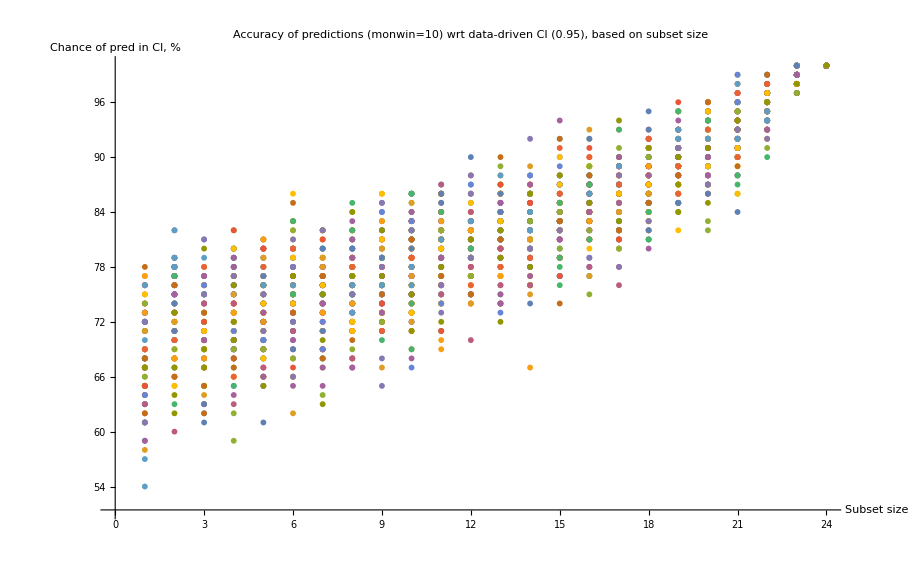

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ reslists100, AxesLabel->{"Subset size", "Chance of pred in CI, %"}, PlotLabel->"Accuracy of predictions (monwin=10) wrt data-driven CI (0.95), based on subset size"]
```

```mathematica
(* for random sampling: *)
```

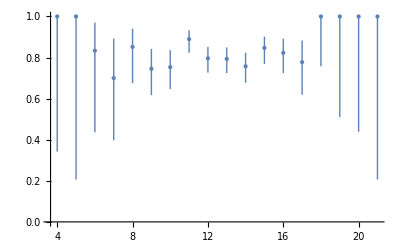

```mathematica
ListPlot[generatePredvsCIOutcomes[1000], PlotStyle->PointSize[Large]]
```

```mathematica
randomOutcomes10000= generatePredvsCIOutcomes[10000]
```

{{3,0.50.40.4},{4,0.570.320.27},{5,0.890.320.09},{6,0.690.120.10},{7,0.700.090.07},{8,0.760.050.04},{9,0.7640.040.032},{10,0.7630.0270.025},{11,0.7870.0230.021},{12,0.8110.0200.019},{13,0.8130.0210.019},{14,0.8160.0220.020},{15,0.8390.0240.022},{16,0.8270.0330.029},{17,0.8510.040.034},{18,0.880.060.04},{19,0.850.130.07},{20,0.800.310.14},{21,1.000000000000000000.40.00000000000000022}}

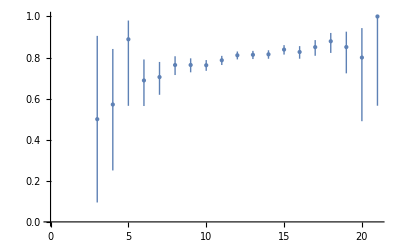

```mathematica
ListPlot[randomOutcomes10000, PlotStyle->PointSize[Large]]
```

```mathematica
randomOutcomes100000= generatePredvsCIOutcomes[100000]
```

{{3,0.570.320.27},{4,0.680.150.12},{5,0.710.070.06},{6,0.7470.040.035},{7,0.7300.0230.022},{8,0.7650.0150.014},{9,0.7740.0110.010},{10,0.7820.0080.008},{11,0.7920.0070.007},{12,0.7990.0060.006},{13,0.8070.0060.006},{14,0.8200.0070.006},{15,0.8370.0070.007},{16,0.8510.0090.009},{17,0.8570.0120.011},{18,0.8680.0190.017},{19,0.8720.0310.026},{20,0.910.050.04},{21,0.880.130.07},{22,1.000000000000000000.320.00000000000000022},{23,1.000000000000000000.60.00000000000000022}}

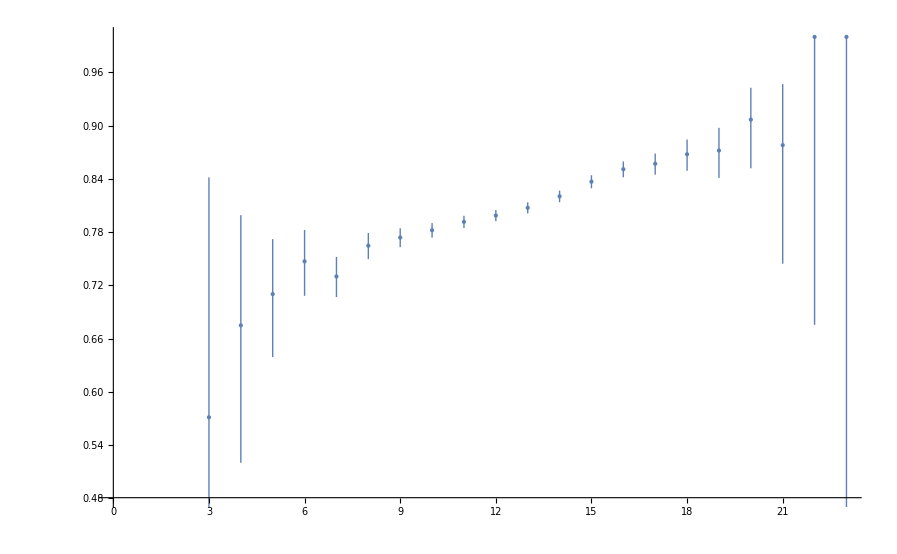

```mathematica
ListPlot[randomOutcomes100000, PlotStyle->PointSize[Large]]
```

```mathematica
(*** COMPARISON: data-driven CI for monitor FNR vs ground truth ***) 
(* an outcome whether GT is in CI interval described by pairlist *) 
oneIntervalGtTest[pairIdList_] := IntervalMemberQ[(* interval *) interWilson[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *) predFNR[0.1, 10]];

(* a pair of interval (described by pairlist) and GT *)
oneIntervalGtTestPair[pairIdList_] := {(* interval *) interWilson[countFromFiles[ "FNcount",monFilenames[10, pairIdList]], countFromFiles[ "h1count",monFilenames[10, pairIdList]], 0.95], (* prediction *)  predFNR[0.1, 10]};
```

```mathematica
(** VISUALS for data-driven CI vs GT **)
```

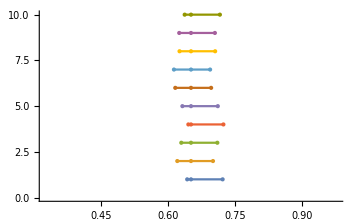

```mathematica
(* large subsets *) 
NumberLinePlot[oneIntervalGtTestPair[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {23,25},{#}] &/@ RandomInteger[{1,subsetCt23to25},10], PlotStyle->PointSize[Large]]
```

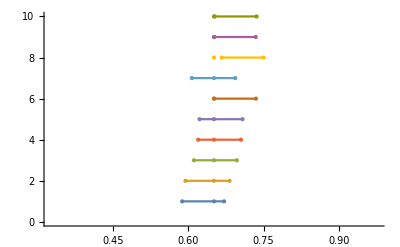

```mathematica
(* medium-large subsets *) 
NumberLinePlot[oneIntervalGtTestPair[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {20,25},{#}] &/@ RandomInteger[{1,subsetCt20to25},10], PlotStyle->PointSize[Large]]
```

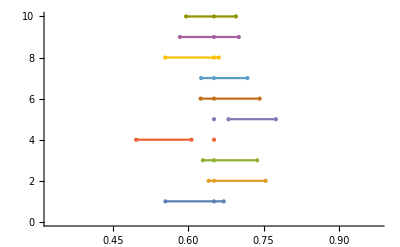

```mathematica
(* all subsets *) 
NumberLinePlot[oneIntervalGtTestPair[#]&/@ Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {1,25},{#}] &/@ RandomInteger[{1,subsetCt},10], PlotStyle->PointSize[Large]]
```

```mathematica
generateGtSuccessCountsPerSubsetSize:= With[{subsetsCt = #},
(* count truths *)Count[oneIntervalGtTest[#]&/@ (* all possible sets of pairs for tests *) Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt},{#}] &/@ (* getting random 100 subsets *)  RandomInteger[{1,(*counting subsets *)Length@Subsets[Flatten[Outer[List, Range[1,5], Range[1,5]], 1], {subsetsCt}]
},100], {True}]
]& /@ Range[1, 24];
```

```mathematica
resGtList2 = {45,54,52,53,60,53,53,54,60,63,53,63,69,57,74,74,81,76,80,75,90,89,95,93};
```

```mathematica
resGtList1 = {61,50,50,55,55,57,60,49,59,51,63,51,62,72,76,79,73,81,71,75,88,85,85,92};
```

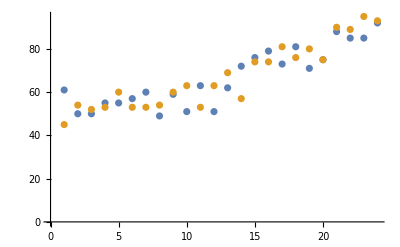

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ {resGtList1, resGtList2}]
```

```mathematica
(* 100 runs of 100 samples each *) 
resGtLists100 = Table[generateGtSuccessCountsPerSubsetSize, 100]
```

```mathematica
resGtLists100 ={{65,58,48,45,61,55,60,57,68,62,65,67,66,65,69,70,70,69,78,78,86,86,92,98},{53,51,57,50,59,61,64,65,63,64,54,62,77,73,73,67,73,72,81,78,83,84,91,98},{53,48,48,56,62,56,56,61,62,58,57,65,75,77,70,66,72,75,78,77,84,81,90,93},{61,50,59,59,66,60,62,60,63,55,57,69,64,64,67,67,83,87,78,81,82,86,88,97},{51,52,47,57,50,61,60,59,61,63,59,67,69,70,68,71,67,79,77,87,78,80,88,98},{63,52,57,65,61,58,57,60,61,66,59,68,72,75,66,72,78,75,76,82,76,88,91,95},{63,52,59,58,60,50,63,57,69,65,65,67,68,63,70,68,79,76,76,82,85,87,92,97},{59,60,58,55,57,59,58,62,58,60,69,63,64,65,72,76,78,75,84,79,80,88,90,99},{58,63,56,64,50,57,64,56,61,71,61,62,68,75,67,71,71,77,81,88,89,85,88,98},{52,56,50,54,61,51,53,60,64,54,70,62,68,76,64,70,68,83,83,85,81,90,95,97},{55,42,53,56,60,52,59,65,53,71,62,63,73,72,73,68,73,73,84,82,85,86,84,96},{56,49,49,56,51,59,55,59,56,60,62,57,68,68,75,69,82,81,74,80,91,82,94,94},{55,63,51,62,56,62,57,65,50,65,65,63,58,68,71,69,74,78,73,79,84,87,90,94},{60,45,53,58,52,59,55,59,63,58,58,64,71,71,68,70,80,77,75,77,83,81,89,92},{55,58,54,55,61,55,52,56,59,71,73,67,66,75,70,65,78,71,73,76,84,87,83,98},{54,54,42,46,52,54,65,63,64,59,68,58,68,72,69,79,77,74,79,79,80,86,88,98},{63,47,62,56,53,59,59,55,54,67,70,69,61,74,69,76,71,79,80,88,86,87,90,92},{58,45,49,66,50,54,62,53,57,64,65,64,68,73,76,71,68,75,77,85,86,86,92,95},{60,52,58,63,55,56,61,44,54,66,60,70,62,65,66,73,80,81,80,81,87,82,88,97},{60,53,58,51,54,60,53,62,56,66,66,62,70,68,69,73,70,76,80,84,82,91,92,95},{58,54,57,59,52,58,58,64,61,66,67,61,69,74,70,72,71,78,73,85,83,87,87,95},{55,60,59,40,60,62,60,51,61,66,59,66,64,74,66,71,77,75,83,81,83,86,89,94},{68,56,54,60,57,53,63,59,54,59,63,67,59,57,71,67,65,64,78,80,83,85,84,99},{55,59,65,49,58,58,59,60,63,55,60,70,72,73,74,77,69,84,86,76,83,87,92,99},{53,63,56,45,58,53,56,64,64,55,70,71,77,76,75,73,78,74,82,85,87,86,89,95},{49,60,52,49,56,58,55,62,60,67,59,65,68,68,73,71,80,78,80,78,83,85,89,96},{51,55,48,57,58,62,57,65,56,64,62,70,69,72,71,72,75,78,80,82,81,84,90,97},{59,47,58,56,58,60,49,59,70,63,66,63,69,68,75,73,76,73,82,75,86,88,88,95},{50,56,61,62,53,55,57,60,70,58,66,68,72,73,67,73,78,84,79,78,88,78,91,93},{52,55,53,62,52,51,63,65,63,62,59,69,65,62,73,68,73,77,73,85,87,91,85,95},{52,61,50,59,59,59,52,62,62,71,63,67,64,60,75,73,81,72,89,81,87,84,88,97},{53,52,57,49,56,59,58,61,61,75,73,68,67,78,67,75,75,73,75,77,87,81,93,95},{57,55,51,53,65,65,63,55,61,74,59,62,69,66,70,69,69,75,80,88,83,89,86,96},{66,66,53,58,65,58,65,62,61,60,62,66,54,75,72,67,75,77,81,80,86,92,93,97},{63,50,54,49,54,55,63,55,55,58,69,66,65,61,69,87,69,77,80,85,81,85,94,97},{54,63,58,56,69,52,67,57,65,73,62,66,64,69,62,74,79,79,86,83,90,87,84,91},{60,54,55,57,53,57,63,52,67,69,61,62,62,67,70,74,70,73,71,81,80,90,89,98},{48,52,54,60,59,54,57,69,63,64,62,63,67,67,74,72,71,79,84,81,85,83,91,93},{46,63,51,56,53,59,59,54,62,74,61,61,67,73,69,63,74,86,76,74,79,85,92,95},{53,51,49,61,56,50,61,54,64,73,62,67,59,74,72,77,76,77,73,84,86,83,93,97},{47,61,54,60,63,53,60,59,60,65,54,66,62,72,64,77,65,72,81,81,88,83,94,96},{61,61,62,54,59,60,66,55,57,63,64,66,60,67,58,78,74,68,81,76,78,87,89,93},{59,57,54,61,54,59,55,66,65,63,67,70,72,71,68,71,76,77,73,88,85,90,91,94},{58,59,60,56,62,54,63,61,61,60,67,69,72,64,70,78,71,79,75,84,85,89,91,98},{60,51,57,58,60,65,56,66,53,65,66,57,76,66,77,69,85,68,84,85,83,81,87,97},{59,57,53,52,51,47,51,60,71,59,59,63,70,61,71,71,71,80,76,79,79,93,90,96},{46,51,60,58,52,43,58,59,60,66,72,68,67,66,70,71,75,72,84,86,85,82,90,97},{54,54,52,59,61,67,61,60,66,57,56,65,68,68,73,78,76,79,84,73,87,89,90,96},{58,55,55,50,59,63,66,64,67,60,66,65,67,70,80,81,76,77,78,78,82,86,87,97},{55,45,62,52,58,61,57,60,62,64,68,64,58,62,74,73,76,75,79,77,81,84,94,99},{63,55,46,54,52,53,59,58,62,59,55,63,61,75,70,76,73,87,76,84,88,89,89,95},{57,60,48,60,56,67,67,58,65,66,49,60,73,68,72,72,75,80,76,82,83,86,87,100},{54,47,54,61,47,59,62,65,55,60,60,63,65,63,72,69,74,74,74,82,88,90,88,100},{45,53,55,54,61,55,65,61,63,56,65,63,62,68,72,72,80,84,84,78,82,92,92,98},{57,49,45,64,55,60,61,67,57,60,65,69,70,64,76,64,73,78,87,84,76,89,92,95},{46,54,56,55,63,51,53,60,62,61,60,56,55,66,65,74,65,78,71,78,75,85,82,99},{52,49,55,62,56,51,54,53,58,58,66,55,72,72,70,75,74,75,83,81,93,83,88,96},{52,58,46,53,58,62,66,65,61,58,63,59,63,54,70,71,76,85,80,81,81,89,92,97},{64,58,54,52,53,58,59,61,57,61,67,68,65,65,64,68,69,78,77,81,86,84,94,95},{50,57,50,55,57,64,62,62,55,69,60,66,68,74,68,66,76,78,75,81,79,85,89,97},{63,55,53,59,51,46,58,60,67,65,63,66,65,71,62,72,72,74,78,87,86,90,85,98},{60,44,42,48,48,62,48,62,53,61,66,68,67,71,72,70,68,80,84,82,90,83,89,97},{58,45,58,62,48,49,60,58,56,64,59,64,62,68,65,74,69,75,74,77,84,89,93,98},{53,56,40,62,61,63,50,62,61,57,61,71,73,71,68,74,69,81,82,77,93,83,89,97},{59,46,53,53,58,58,47,58,67,66,66,61,63,63,68,72,82,84,77,86,87,89,86,96},{58,55,51,54,57,56,60,58,67,72,74,61,63,67,72,70,72,72,79,80,86,78,89,94},{57,57,51,55,54,58,61,65,66,54,57,59,80,72,71,72,73,80,72,82,87,88,90,93},{51,60,43,54,54,59,59,64,71,61,59,68,69,63,73,71,73,74,78,75,85,88,87,94},{53,58,51,52,71,64,55,61,65,54,62,61,72,64,68,71,81,74,85,80,82,87,88,95},{59,60,54,59,50,62,57,61,60,61,64,59,65,75,65,76,71,67,81,81,90,84,86,98},{55,55,54,57,52,62,59,63,64,58,57,61,72,69,68,75,80,77,83,84,86,82,94,98},{56,58,58,64,59,58,55,67,64,67,68,66,57,73,80,71,74,79,78,80,79,84,93,93},{52,60,51,46,60,64,61,66,55,67,68,64,60,75,62,78,67,79,83,84,85,88,93,94},{53,58,51,53,63,58,59,69,62,63,66,67,72,70,68,74,79,74,87,80,86,90,93,95},{56,50,58,58,46,59,60,65,48,63,64,63,58,68,68,72,70,84,80,83,81,81,87,97},{58,56,66,47,52,57,55,62,58,63,65,67,62,65,77,65,68,82,82,84,86,83,89,98},{56,52,66,51,60,61,52,65,60,66,63,64,69,70,66,72,82,74,76,80,88,86,92,97},{53,46,59,49,55,63,58,66,60,55,68,66,63,79,78,75,75,75,82,84,84,87,90,98},{59,56,57,50,56,61,63,52,67,66,67,64,68,65,72,78,81,71,78,83,90,84,86,91},{53,53,55,51,57,50,58,61,61,56,68,67,66,73,78,76,72,79,80,75,81,84,93,98},{56,56,48,56,60,59,52,55,63,58,56,63,74,63,73,69,79,81,71,79,85,83,88,96},{56,47,62,53,60,56,60,60,61,66,67,66,74,73,65,74,75,77,74,82,84,84,86,99},{53,56,49,56,60,62,52,60,61,60,54,71,66,75,67,82,75,78,79,86,82,89,88,98},{62,53,66,58,59,54,55,52,56,54,61,63,71,70,72,63,79,78,78,87,77,87,88,92},{54,54,55,58,43,61,59,60,59,62,56,75,63,64,65,72,74,78,82,80,88,91,85,94},{59,52,53,57,65,54,61,62,61,65,59,60,65,70,69,73,70,78,84,82,88,88,92,97},{54,49,54,62,48,54,64,63,51,59,72,68,68,79,74,71,75,82,77,82,89,88,91,89},{51,58,52,62,59,50,59,63,54,66,66,60,74,67,73,70,70,74,77,78,81,94,95,97},{52,63,58,54,57,62,58,55,56,64,61,66,66,63,73,75,78,81,78,78,82,87,88,96},{55,58,58,61,56,48,55,61,61,66,69,69,66,76,71,69,75,71,83,76,79,84,87,94},{55,50,62,59,61,55,58,58,73,64,68,66,68,72,71,70,79,73,71,81,80,82,85,95},{55,46,53,67,49,62,64,66,63,56,59,65,69,62,68,78,77,75,83,85,87,86,85,99},{53,51,57,53,60,58,58,62,63,61,58,64,62,76,73,76,75,72,80,85,76,92,86,94},{56,60,59,46,56,54,55,55,58,52,68,64,68,66,75,67,78,77,78,87,88,90,94,93},{62,49,57,49,54,60,61,56,68,66,65,67,66,71,59,71,71,77,78,74,83,88,83,99},{63,55,59,49,62,57,60,57,63,67,61,77,73,63,70,80,86,74,77,79,80,87,93,93},{52,54,44,61,56,62,66,64,69,64,59,71,61,79,81,79,66,82,78,85,83,90,91,97},{57,56,49,59,56,57,61,58,61,65,68,55,72,74,72,68,76,71,78,80,86,87,85,94},{56,59,54,59,55,59,67,72,63,62,68,64,59,73,73,75,73,72,79,82,85,80,89,98},{48,52,54,54,52,58,68,59,66,68,70,64,65,64,68,72,73,83,82,84,86,86,86,94}}
```

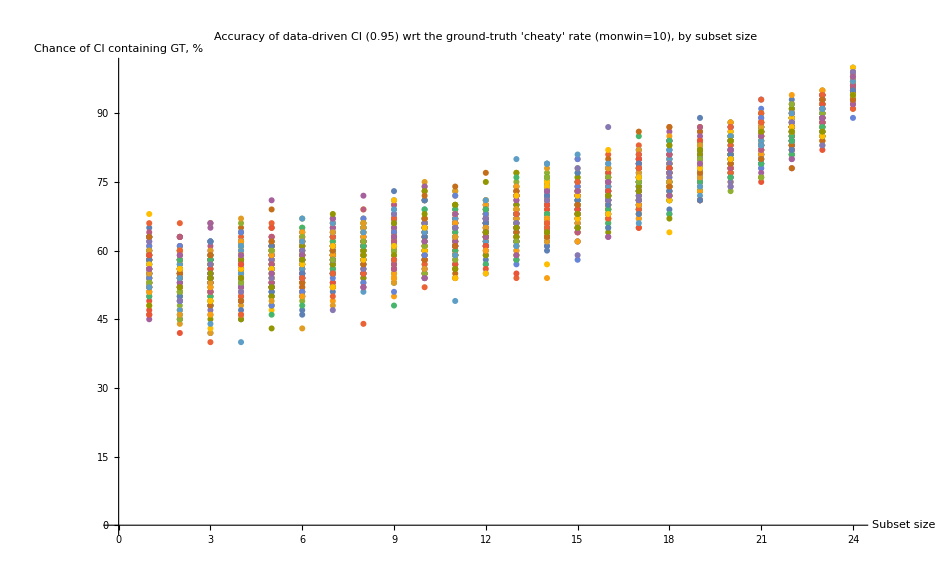

```mathematica
ListPlot[Inner[List, Range[1,24], #, List]& /@ resGtLists100, AxesLabel->{"Subset size", "Chance of CI containing GT, %"}, PlotLabel->"Accuracy of data-driven CI (0.95) wrt the ground-truth 'cheaty' rate (monwin=10), by subset size"]
```